```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica"];
Get["ctmc`"]
Get["utils`"]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 6 binding sites ***)

HomeDir="/home/tohme/.julia/dev/LLROpt/";
circuitData=Import[HomeDir<>"spec/circuits.json","RawJSON"];

circuitId="6bs";
edges2=circuitData[circuitId]["edges"];
weights2=ToExpression[circuitData[circuitId]["weight_labels"]];
nstates2=circuitData[circuitId]["nstates"];
vertexPartition=circuitData[circuitId]["vertex_partition"];
nedges2=Length[edges2];
offInd=circuitData[circuitId]["off_indicator"];
onInd=1-offInd;
```

```mathematica
weightsMgr=weights2/.{kuoff1->0,kuoff2->0,kuoff2->0,kuoff3->0,kuoff4->0,kuoff5->0,kuoff6->0,kon1->0,kon2->0,kon3->0,kon4->0,kon5->0,kon6->0,koff2->0,koff3->0,koff4->0,koff5->0,koff6->0,koff7->0,kboff1->kdl,kboff2->kdl,kboff3->kdl,kboff4->kdl,kboff5->kdl,kboff6->kdl,koff1->5,kon7->5,kbon1->0,kbon2->0,kbon3->0,kbon4->0,kbon5->0,kbon6->0,kuon1->5,kuon2->10,kuon3->15,kuon4->20,kuon5->25,kuon6->30};
```

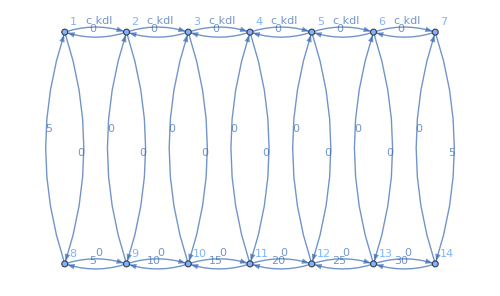

```mathematica
(*Plot the circuit*)edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weightsMgr)[[i]],0.55],{i,1,nedges2}],ImageSize->500,GraphLayout->{"MultipartiteEmbedding","VertexPartition"->vertexPartition}]
```

```mathematica
Q2 = RateMatrix[edges2, weightsMgr, nstates2];
ss2 = SteadyStateProbabilities[Q2];
(*Variance rate*)
var=VarianceRate[Q2,onInd];
(*Sharpness*)
piOn=onInd.ss2;
dpiOn=D[piOn,{c,1}];
sharp=c*dpiOn;
```

```mathematica
(*Fisher information rate with accumulated decoding*)FisherRateAcc=sharp^2/var;
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {1,2,3,4,5,6,7};
onStates = {8,9,10,11,12,13,14};
Foff = LaplaceTransformToSetByState[Q2,1,onStates,s1];
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[Foff[[7]][[1]], {s1,1}]]];

meanToffLt = -partials1;
meanTon=2/5+1/10+1/15+1/20+1/25+1/30;
τ = Simplify[meanToffLt + meanTon,assum];
```

```mathematica
Foff[[7]][[1]];
Poff=InverseLaplaceTransform[Foff[[7]][[1]],s1,t1]//Simplify
```

-1/(24 (-5+c kdl)^6)c^6 kdl^6 (-120 ⅇ^(-5 t1)+120 ⅇ^(-c kdl t1)+120 ⅇ^(-c kdl t1) (-5+c kdl) t1+60 ⅇ^(-c kdl t1) (-5+c kdl)^2 t1^2+20 ⅇ^(-c kdl t1) (-5+c kdl)^3 t1^3+5 ⅇ^(-c kdl t1) (-5+c kdl)^4 t1^4+ⅇ^(-c kdl t1) (-5+c kdl)^5 t1^5)

```mathematica
integrand =D[Poff,{c,1}]^2/Poff;
```

```mathematica
integrandNum[t1_?NumericQ,c_?NumericQ,kdl_?NumericQ,kon7_?NumericQ]:=Evaluate[integrand/τ]
```

```mathematica
NIntegrate[integrandNum[t1,c,kon7*γ/c,kon7]*c^2/.{γ->1.43,kon7->5,c->42},{t1,0,∞}]
```

2.59455

```mathematica
FisherRateAcc/.{kdl->kon7*γ2/c}/.{γ2->1.52,kon7->5.,c->42.}
```

1.06393

```mathematica
integrandNum[1,c,kon7*γ/c,kon7]*c^2/.{γ->0.5,kon7->5,c->1000}
```

0.440628